# Notebook 03: Transforming Graphics and Drawing Curves

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Example: Radio Tower

Suppose we want to draw a radio tower. We can start by drawing a few lines to get the basic shape, and put a little ball on top.

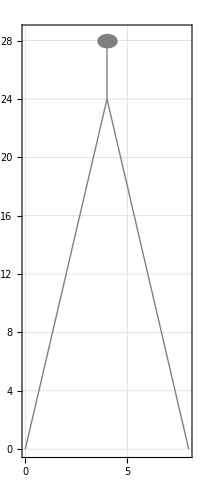

```mathematica
Graphics[{Gray,Thick,Line[{{0,0},{4,24},{8,0}}],Line[{{4,24},{4,28}}],Disk[{4,28},1/2]},Frame->True,GridLines->Automatic]
```

We can add some radio waves by drawing concentric circles of thin, dot-dashed lines. (When we are done with the dashing we turn it off with Dashing[None]). These circles will all have the same centre point and differing radii.

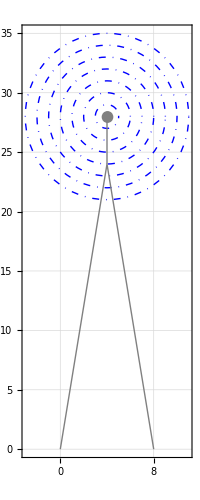

```mathematica
Graphics[{Blue,DotDashed,Table[Circle[{4,28},r],{r,1,7}],Gray,Thick,Dashing[None],Line[{{0,0},{4,24},{8,0}}],Line[{{4,24},{4,28}}],Disk[{4,28},1/2]},Frame->True,GridLines->Automatic]
```

We can turn our commands into a drawing function with relative coordinates.

```mathematica
drawRadioTower[{x_,y_}]:=
{Blue,DotDashed,Table[Circle[{x+4,y+28},r],{r,1,7}],Gray,Thick,Dashing[None],Line[{{x,y},{x+4,y+24},{x+8,y}}],Line[{{x+4,y+24},{x+4,y+28}}],Disk[{x+4,y+28},1/2]}
```

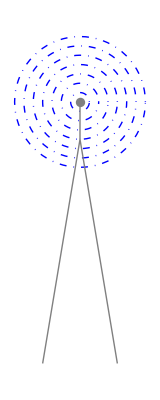

```mathematica
Graphics[drawRadioTower[{0,0}]]
```

## The Scale command

The Scale command allows us to change the size of an object, either uniformly, or by different factors along different axes.

```mathematica
drawUFO[{x_,y_}]:=
{Orange,Disk[{x,y},{3,1}],LightOrange,Disk[{x,y+1/2},{3/2,1}]}
```

In the image below, I’ve drawn our original UFO, one that is uniformly scaled to half the size and one that is uniformly scaled to twice the size.

```mathematica
Graphics[{drawUFO[{0,0}],Scale[drawUFO[{7,0}],1/2],Scale[drawUFO[{16,0}],2]},Frame->True,GridLines->Automatic]
```

-Graphics-

To make something narrower or wider while maintaining its height, we scale along the x axis but not the y axis. (That is, we set the y axis scaling multiple to 1, so it is neither larger nor smaller than the original).

```mathematica
Graphics[{drawUFO[{0,0}],Scale[drawUFO[{7,0}],{1/2,1}],Scale[drawUFO[{16,0}],{2,1}]},Frame->True,GridLines->Automatic]
```

-Graphics-

To make something taller or shorter while maintaining its width, we scale along the y axis but not the x axis.

```mathematica
Graphics[{drawUFO[{0,0}],Scale[drawUFO[{7,0}],{1,1/2}],Scale[drawUFO[{16,0}],{1,2}]},Frame->True,GridLines->Automatic]
```

-Graphics-

### Scaling a complex graphic element

We can wrap the Scale command around any drawing function to create scaled copies.

```mathematica
Graphics[{LightGray,Rectangle[{-2,-2},{50,15}],drawRadioTower[{0,0}],Scale[drawRadioTower[{20,0}],1/2],Scale[drawRadioTower[{33,0}],1/4],Scale[drawRadioTower[{39,0}],1/8]}]
```

-Graphics-

In this example we also see how to get a perspective effect (things that are farther away appear smaller).

## The Translate command

The Translate command allows us to move an element along the x axis, y axis or both.

Here is a blue disk, along with a green disk that has been translated 2 units along the x axis (i.e., to the right), and a red disk that has been translated -3 units along the same axis (i.e., to the left). Note that the coordinates given to all three disks are {0, 0}. Their relative movement is caused by the Translate command.

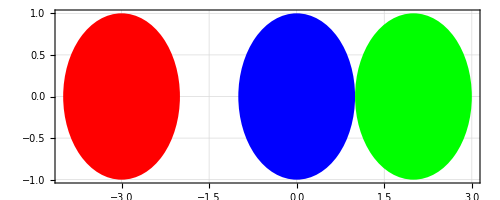

```mathematica
Graphics[{Blue, Disk[{0,0},1], Green, Translate[Disk[{0,0},1],{2,0}],Red,Translate[Disk[{0,0},1],{-3,0}]},Frame->True,GridLines->Automatic]
```

The pair of coordinates given to the Translate command is often referred to as a ‘vector’, and visualized with an arrow. In the figure below, the translation vector is {3, 4}.

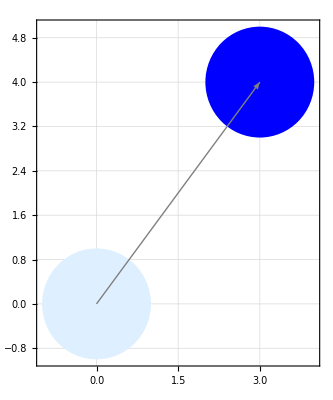

```mathematica
Graphics[{LightBlue, Disk[{0,0},1], Blue, Translate[Disk[{0,0},1],{3,4}],Gray,Thick,Arrow[{{0,0},{3,4}}]},Frame->True,GridLines->Automatic]
```

We don’t have to translate elements from the origin. Compare this figure with the previous one: note the difference in centre coordinates for the two disks, and note how we adjusted the position of the arrow.

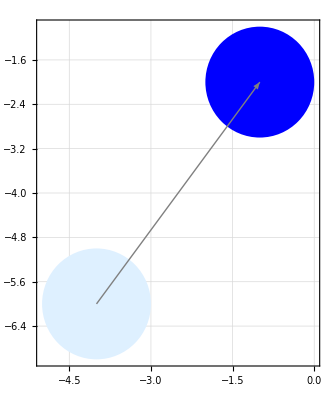

```mathematica
Graphics[{LightBlue, Disk[{-4,-6},1], Blue, Translate[Disk[{-4,-6},1],{3,4}],Gray,Thick,Arrow[{{-4,-6},{-4+3,-6+4}}]},Frame->True,GridLines->Automatic]
```

## The Rotate command

The Rotate command allows us to rotate an element by a specified angle. We can use either degrees or radians to specify the angle.

Here are 4 UFOs. The second, third and fourth are rotated 45, 90 and 135 degrees respectively.

```mathematica
Graphics[{drawUFO[{0,0}],Rotate[drawUFO[{10,0}],45Degree],Rotate[drawUFO[{20,0}],90Degree],Rotate[drawUFO[{30,0}],135 Degree]},Frame->True,GridLines->Automatic]
```

-Graphics-

Note that angles are measured from a horizontal line and increase in a counterclockwise manner. If we want to rotate in the clockwise direction, we specify negative angles.

```mathematica
Graphics[{drawUFO[{0,0}],Rotate[drawUFO[{10,0}],-45Degree],Rotate[drawUFO[{20,0}],-90Degree],Rotate[drawUFO[{30,0}],-135 Degree]},Frame->True,GridLines->Automatic]
```

-Graphics-

## Tables of Transformations

By using the Table command with various transformations, we can make many interesting designs.

Rotate an ellipse

```mathematica
Graphics[{Blue,Table[Rotate[Circle[{0,0},{3,1}],r Degree],{r,0,330,30}]}]
```

-Graphics-

Translate an elliptical disk

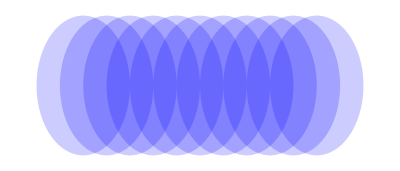

```mathematica
Graphics[{Blue,Opacity[.2],Table[Translate[Disk[{0,0},{2,3}],{x,0}],{x,0,10}]}]
```

Scale a rectangle

```mathematica
Graphics[{Blue,Opacity[.2],Table[Scale[Rectangle[{0,0},{2,3}],s],{s,1,9}]}]
```

-Graphics-

Combining Scale and Rotate

```mathematica
Graphics[{Blue,Opacity[.2],Table[Rotate[Scale[Rectangle[{0,0},{2,3}],s],s*15Degree],{s,1,9}]}]
```

-Graphics-

```mathematica
Graphics[{Blue,Table[Rotate[Scale[Circle[{0,0},{2,3}],s],s*15Degree],{s,1,9}]}]
```

-Graphics-

## The BezierCurve command

There are a couple of different ways to draw curved lines with the Graphics command. One is to use the BezierCurve command.

To specify a Bézier curve, you need to include both points on the line and control points. Here is a specification for a curve that opens upward. The points {0, 0} and {3, 0} are endpoints on the curve, drawn in red. The other two points are control points, drawn in blue. Note that the control points do not lie on the curve.

```mathematica
concaveUp={{0,0},{1,-1},{2,-1},{3,0}};
```

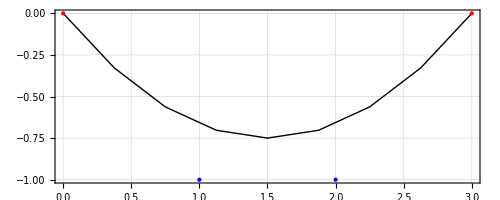

```mathematica
Graphics[{BezierCurve[concaveUp],PointSize[Large],Red,Point[{{0,0},{3,0}}],Blue,Point[{{1,-1},{2,-1}}]},Frame->True,GridLines->Automatic]
```

If we move both control points down, the curve becomes deeper.

```mathematica
concaveUpDeeper={{0,0},{1,-3},{2,-3},{3,0}};
```

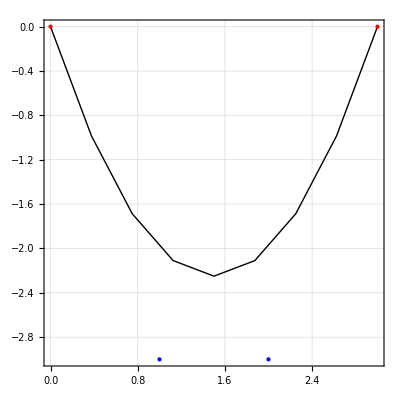

```mathematica
Graphics[{BezierCurve[concaveUpDeeper],PointSize[Large],Red,Point[{{0,0},{3,0}}],Blue,Point[{{1,-3},{2,-3}}]},Frame->True,GridLines->Automatic]
```

If we move the control points closer to the endpoints, the curve becomes broader.

```mathematica
concaveUpBroader={{0,0},{.25,-3},{2.75,-3},{3,0}};
```

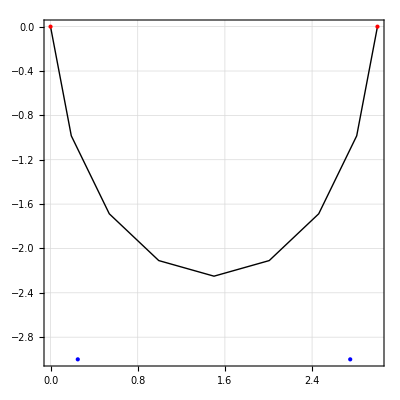

```mathematica
Graphics[{BezierCurve[concaveUpBroader],PointSize[Large],Red,Point[{{0,0},{3,0}}],Blue,Point[{{.25,-3},{2.75,-3}}]},Frame->True,GridLines->Automatic]
```

If the control points are above the line, we end up with a curve that opens downward.

```mathematica
concaveDown={{0,0},{1,1},{2,1},{3,0}};
```

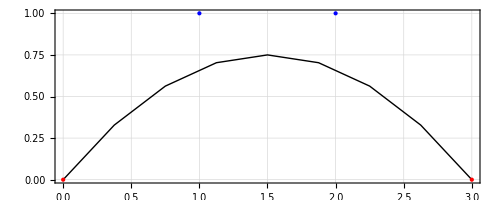

```mathematica
Graphics[{BezierCurve[concaveDown],PointSize[Large],Red,Point[{{0,0},{3,0}}],Blue,Point[{{1,1},{2,1}}]},Frame->True,GridLines->Automatic]
```

It helps to visualize what the control points are doing to the curve if we plot a line through them. Here the line through the control points is drawn in purple.

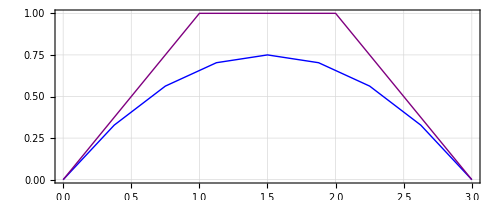

```mathematica
Graphics[{Blue,BezierCurve[concaveDown],Purple,Line[concaveDown]},Frame->True,GridLines->Automatic]
```

If we place one control point above the line and one below it, we can get an S-shape. All points are shown in Red in the following figure.

```mathematica
sShape={{0,0},{1,-1},{2,1},{3,0}};
```

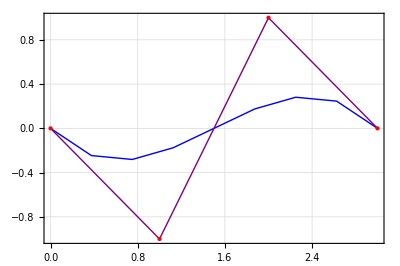

```mathematica
Graphics[{Blue,BezierCurve[sShape],Purple,Line[sShape],PointSize[Large],Red,Point[sShape]},Frame->True,GridLines->Automatic]
```

If you have ever used the ink pen tool in a vector graphics program like Adobe Illustrator, you were drawing with Bézier curves.

## Composite and closed Bézier curves

### Composite curves

We can join multiple curves together by using a longer list of points. The first point is on the curve, the next two are control points, the fourth point is on the curve, the next two are control points, the seventh point is on the curve, and so on. The image below shows a composite curve in blue and a purple line through its control points.

```mathematica
compositeCurve={{0,0},{1,1},{2,-1},{3,0},{5,2},{6,-1},{7,3}};
```

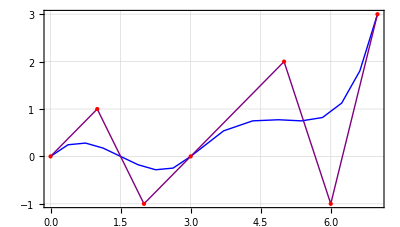

```mathematica
Graphics[{Blue,BezierCurve[compositeCurve],Purple,Line[compositeCurve],PointSize[Large],Red,Point[compositeCurve]},Frame->True,GridLines->Automatic]
```

If the control points to the left and right of a point that lies on a composite line are both on the same side, the curve comes to a sharp point. Look at the point at {3, 0} in the following image.

```mathematica
sharpAngle={{0,0},{1,1},{2,1},{3,0},{4,1},{5,0},{6,1}};
```

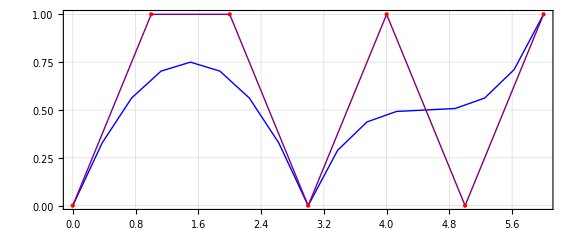

```mathematica
Graphics[{Blue,BezierCurve[sharpAngle],Purple,Line[sharpAngle],PointSize[Large],Red,Point[sharpAngle]},Frame->True,GridLines->Automatic,ImageSize->Large]
```

### Closed curves

By default, the last point on a Bézier curve is not connected to the first one. You can change this behaviour by setting the SplineClosed attribute to true. This allows you to draw closed figures like the one shown below.

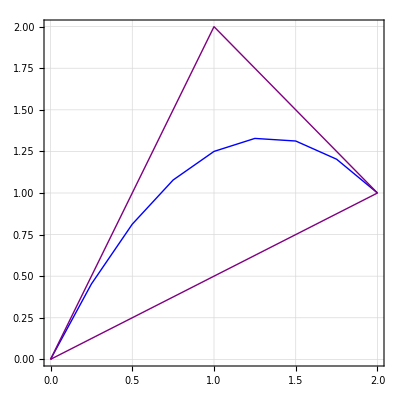

```mathematica
Graphics[{Blue,BezierCurve[{{0,0},{1,2},{2,1}},SplineClosed->True],Purple,Line[{{0,0},{1,2},{2,1},{0,0}}]},Frame->True,GridLines->Automatic]
```

## Line thickness, dashing and edges

The Thickness command allows us to specify line thickness. Note how Table is used here to create a list of images.

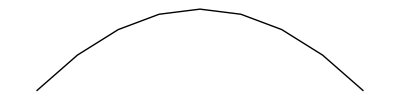
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{Thickness[i],BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{Tiny,Small,Medium,Large}}]
```

A different version of Thickness allows us to specify what proportion of the overall image the thickness of the line should take up.

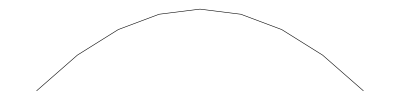
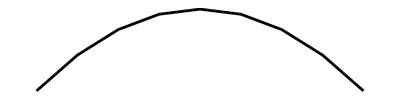
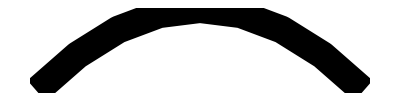
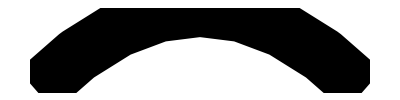

```mathematica
Table[Graphics[{Thickness[i],BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{.001,.005,.05,.1}}]
```

We have seen that we can specify different kinds of lines with commands like Dotted and Dashed.

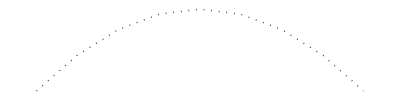
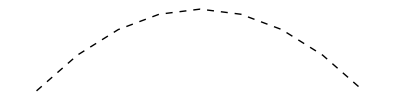
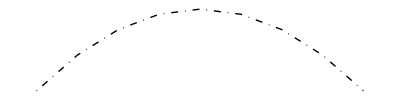
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{i,BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{Dotted,Dashed,DotDashed,Dashing[None]}}]
```

The Dashing command allows us to specify scaled lengths for the line segments and spaces between them.

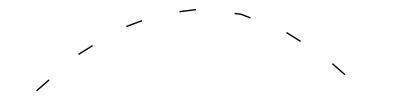
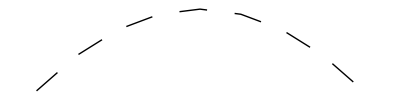
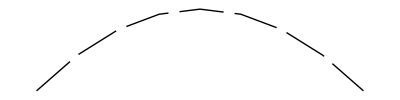
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{Dashing[{i,0.1-i}],BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{.01,.03,.05,.08}}]
```

The CapForm command determines the shape of the ends of lines.

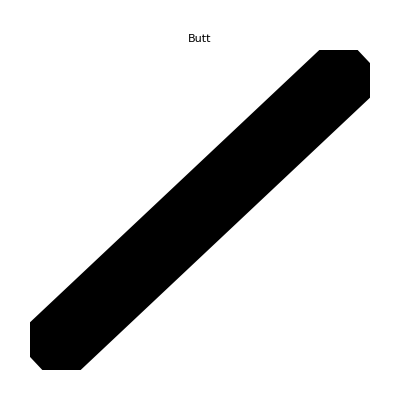
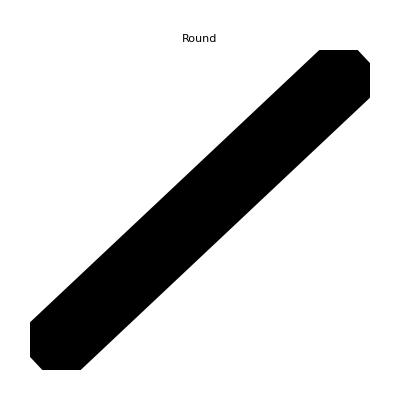
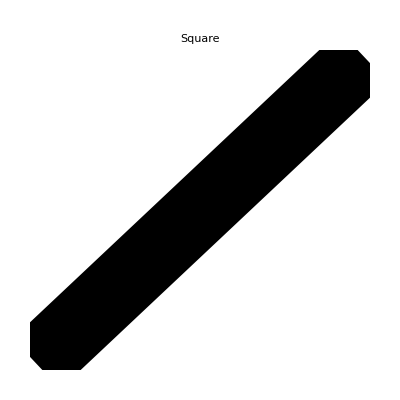

```mathematica
Table[Graphics[{CapForm[cap],Thickness[.2],Line[{{-1,-1},{1,1}}]},PlotLabel->cap,ImagePadding->20],{cap,{"Butt","Round","Square"}}]
```

The JoinForm command determines the shape when lines meet.

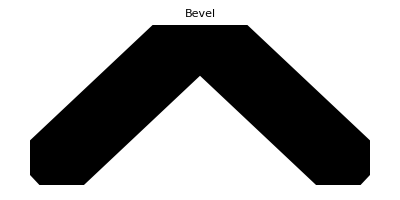
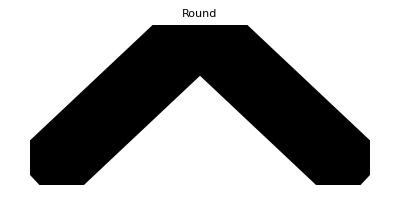
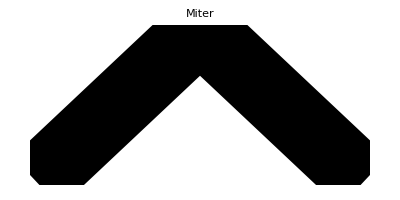

```mathematica
Table[Graphics[{JoinForm[j],Thickness[.2],Line[{{-1,-0.5},{0,0.5},{1,-0.5}}]},PlotLabel->j,ImagePadding->20],{j,{"Bevel","Round","Miter"}}]
```

## Tables of Curves

We can ‘morph’ between a straight line and a curve by using Table to plot a series of intermediate curves. We need to use PlotRange here to focus on the figure, because otherwise Graphics includes space for the control points, even though they aren’t being plotted.

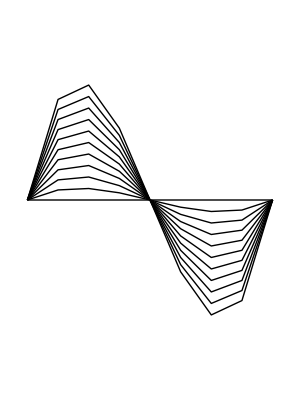

```mathematica
Graphics[Table[BezierCurve[{{0,0},{1,u},{2,-u},{3,0}}],{u,0,5,.5}],PlotRange->{-2,2}]
```

Here is what the above figure looks like if we plot all the control points, too.

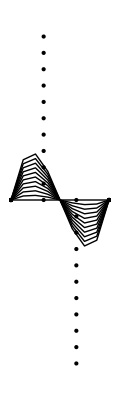

```mathematica
Graphics[{Table[{BezierCurve[{{0,0},{1,u},{2,-u},{3,0}}],Point[{{0,0},{1,u},{2,-u},{3,0}}]},{u,0,5,.5}]}]
```

## Tables of Transformed Curves

We can make flower- and pinwheel-like shapes by rotating closed Bézier curves.

```mathematica
Graphics[Table[Rotate[BezierCurve[{{0,0},{1,2},{2,0}},SplineClosed->True],r Degree],{r,0,315,45}]]
```

-Graphics-

```mathematica
Graphics[Table[Rotate[BezierCurve[{{0,0},{1,2},{1,3},{1.5,1}},SplineClosed->True],r Degree],{r,0,360,24}]]
```

-Graphics-

Altering line thickness and opacity can produce interesting results. Note the use of the ImagePadding attribute here.

```mathematica
Graphics[{Pink,Thickness[.1],Opacity[.2],Table[Rotate[BezierCurve[{{0,0},{0,2},{2,0}},SplineClosed->True],r Degree],{r,0,315,45}]},ImagePadding->22]
```

-Graphics-

```mathematica
Graphics[{Blue,Thickness[.02],Opacity[.15],JoinForm["Round"],Table[Rotate[BezierCurve[{{0,0},{0,2},{-1,0}},SplineClosed->True],r Degree],{r,0,345,15}]}]
```

-Graphics-

## In-Class Activity

### Draw a picture using the Graphics command. Use Scale, Rotate and Translate in your picture. Use the BezierCurve command to include some curved lines.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course